```mathematica
g=0.2573
```

0.2573

```mathematica
T[rh_,μ_]:=1/(π rh)(1-1/2 μ^2 rh^2)
```

```mathematica
f[r_,rh_,μ_]:=1-(1/rh^4+μ^2/rh^4)r^4+ μ^4/rh^4 r^6
```

SetDelayed::write: Interpolation[{{{0.01,2.09258×10^-29},{0.055,0.000010183},{0.075,0.000430536},{0.085,0.00174933},{0.095,0.00494086},{0.097,0.00558436},{0.098,0.00607962},{0.099,0.00663335},{0.1,0.00721134},{0.108,0.0132992},«26»}}][«1»] 中的标签 Interpolation 被保护.

SetDelayed::write: Interpolation[{{{{0.03,5.97552×10^-35},{0.05,3.27222×10^-7},{0.08,1.70091×10^-43},{0.09,9.50832×10^-39},{0.095,9.48736×10^-37},{0.1,0.00658589},{0.108,0.0129285},{0.115,0.0208441},{0.125,0.0355756},{0.15,0.0942373},«15»}}}][«1»] 中的标签 Interpolation 被保护.

SetDelayed::write: Interpolation[{{{0.03,5.97552×10^-35},{0.05,3.27222×10^-7},{0.08,1.70091×10^-43},{0.09,9.50832×10^-39},{0.095,9.48736×10^-37},{0.1,0.00658589},{0.15,0.0942373},{0.2,0.226386},{0.225,0.278783},{0.235,0.297844},«11»}}][r_,rh_,μ_] 中的标签 Interpolation 被保护.

```mathematica
w[r_]:=2.94 Sin[1.24 Sin[0.47 r+1.94]-9.55]+3.53
```

```mathematica
ET[r0_,rh_,μ_]:=2g NIntegrate[w[r]/r^2√(1+f[r,rh,μ]((w[r0]^2/r0^4 *f[r0,rh,μ]^2)/(w[r]^2/r^4*f[r,rh,μ]^2*f[r0,rh,μ]-w[r0]^2/r0^4*f[r0,rh,μ]^2*f[r,rh,μ])))-w[0]/r^2-w'[0]/r,{r,0,r0}]-2 g/r0*w[0]+2*g*w'[0]*Log[r0]
```

```mathematica
L[r0_,rh_,μ_]:=Exp[-1/(2*1/(π rh)(1-1/2 μ^2 rh^2))*(2g NIntegrate[w[r]/r^2√(1+f[r,rh,μ]((w[r0]^2/r0^4 *f[r0,rh,μ]^2)/(w[r]^2/r^4*f[r,rh,μ]^2*f[r0,rh,μ]-w[r0]^2/r0^4*f[r0,rh,μ]^2*f[r,rh,μ])))-w[0]/r^2-w'[0]/r,{r,0,r0}]-2 g/r0*w[0]+2*g*w'[0]*Log[r0])]
```

```mathematica
w[0]
```

1.0077

```mathematica
numericSolution=NSolve[T[rh0,0]==0.01,rh0]
```

{{}}

```mathematica
numericSolution=NSolve[T[rh0,0]==0.01,rh0]
```

{{rh0→31.831}}

```mathematica
rh0=31.830988618379067
```

31.831

```mathematica
data=Table[{r0,ET[r0,31.830988618379067,0]},{r0,0,4,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
ET[3,31.830988618379067,0]//N
```

1.16042

```mathematica
r0=4
```

4

```mathematica
numericSolution=NSolve[T[rh1,0]==0.05,rh1]
```

{{rh1→6.3662}}

```mathematica
rh1=6.366197723675813
```

6.3662

```mathematica
ET[3,6.366197723675813,0]//N
```

1.3642

```mathematica
r1=4
```

4

```mathematica
numericSolution=NSolve[T[rh2,0]==0.1,rh2]
```

{{rh2→3.1831}}

```mathematica
rh2=3.1830988618379066
```

3.1831

```mathematica
ET[2.451,3.1830988618379066,0]//N
```

0.552181

```mathematica
data=Table[{r0,ET[r0,3.1830988618379066,0]},{r0,0,4,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {3.18241436603993978725346547520302920020185410976409912109375} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.955406+0.00524006 ⅈ 和 0.0000100685.

NIntegrate::ncvb: 在接近 {r} = {3.18130072025424} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.941384+0.0128096 ⅈ 和 0.0000143298.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {3.1802956352444} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.928901+0.0203589 ⅈ 和 0.0000144612.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r2=2.5
```

2.5

```mathematica
numericSolution=NSolve[T[rh3,0]==0.15,rh3]
```

{{rh3→2.12207}}

```mathematica
rh3=2.1220659078919377
```

2.12207

```mathematica
ET[1.691,2.1220659078919377,0]//N
```

0.232926

```mathematica
data=Table[{r0,ET[r0,2.1220659078919377,0]},{r0,0,3,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {2.12162861239237} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.617957+0.00872431 ⅈ 和 0.0000116562.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {2.12019709016293} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.598841+0.0196806 ⅈ 和 0.0000141729.

NIntegrate::ncvb: 在接近 {r} = {2.1217859717513} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.581812+0.0305737 ⅈ 和 7.93802×10^-6.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r3=1.74
```

1.74

```mathematica
numericSolution=NSolve[T[rh4,0]==0.2,rh4]
```

{{rh4→1.59155}}

```mathematica
rh4=1.5915494309189533
```

1.59155

```mathematica
ET[1.28,1.5915494309189533,0]//N
```

-0.0142585

```mathematica
data=Table[{r0,ET[r0,1.5915494309189533,0]},{r0,0,1.5,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
r4=1.33
```

1.33

```mathematica
numericSolution=NSolve[T[rh5,0]==0.25,rh5]
```

{{rh5→1.27324}}

```mathematica
rh5=1.2732395447351628
```

1.27324

```mathematica
ET[1.025,1.2732395447351628,0]//N
```

-0.162139

```mathematica
data=Table[{r0,ET[r0,1.2732395447351628,0]},{r0,0,1.5,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {1.27252028810169} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.334544+0.0125696 ⅈ 和 0.0000148158.

NIntegrate::ncvb: 在接近 {r} = {1.27307158305078} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.304191+0.0310485 ⅈ 和 8.08335×10^-6.

NIntegrate::ncvb: 在接近 {r} = {1.27199215582258} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.277656+0.0493861 ⅈ 和 0.0000219567.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

0.0446448

```mathematica
r5=1.07
```

1.07

```mathematica
numericSolution=NSolve[T[rh6,0]==0.3,rh6]
```

{{rh6→1.06103}}

```mathematica
rh6=1.0610329539459689
```

1.06103

```mathematica
ET[0.86,1.0610329539459689,0]//N
```

-0.28428

```mathematica
data=Table[{r0,ET[r0,1.0610329539459689,0]},{r0,0,1.1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {1.06009854508147} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.253428+0.0210691 ⅈ 和 0.0000158013.

NIntegrate::ncvb: 在接近 {r} = {1.05982134568015} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.217585+0.044378 ⅈ 和 0.0000118135.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {1.0602640425965} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.185938+0.0674885 ⅈ 和 0.0000231292.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

```mathematica
r6=0.89
```

0.89

```mathematica
numericSolution=NSolve[T[rh7,0]==0.35,rh7]
```

{{rh7→0.909457}}

```mathematica
rh7=0.9094568176679734
```

0.909457

```mathematica
ET[0.739,0.9094568176679734,0]//N
```

-0.393042

```mathematica
data=Table[{r0,ET[r0,0.9094568176679734,0]},{r0,0,1.1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.9092562247621169837195898022486062473035417497158050537109375} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.247282+0.00160961 ⅈ 和 5.89295×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.909149253914805} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.193042+0.0311209 ⅈ 和 0.0000196754.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.908627641938754} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.15032+0.0603686 ⅈ 和 0.0000254547.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r7=0.77
```

0.77

```mathematica
numericSolution=NSolve[T[rh8,0]==0.4,rh8]
```

```mathematica
data=Table[{r0,ET[r0,0.7957747154594766,0]},{r0,0,3,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.795325180063559} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.333491+0.0118005 ⅈ 和 0.0000138795.

NIntegrate::ncvb: 在接近 {r} = {0.794866009260113} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.286417+0.0394499 ⅈ 和 0.0000104598.

NIntegrate::ncvb: 在接近 {r} = {0.795304678618977} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.246281+0.0667082 ⅈ 和 0.0000102527.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
numericSolution=NSolve[T[rh9,0]==0.4,rh9]
```

```mathematica
data=Table[{r0,ET[r0,0.7957747154594766,0]},{r0,0,3,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.795325180063559} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.333491+0.0118005 ⅈ 和 0.0000138795.

NIntegrate::ncvb: 在接近 {r} = {0.794866009260113} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.286417+0.0394499 ⅈ 和 0.0000104598.

NIntegrate::ncvb: 在接近 {r} = {0.795304678618977} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.246281+0.0667082 ⅈ 和 0.0000102527.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
rh8=0.7957747154594766
```

0.795775

```mathematica
ET[0.649,0.7957747154594766,0]//N
```

-0.494024

```mathematica
data=Table[{r0,ET[r0,0.7957747154594766,0]},{r0,0,1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.795325180063559} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.184156+0.0152722 ⅈ 和 0.0000184798.

NIntegrate::ncvb: 在接近 {r} = {0.794866009260113} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.126866+0.0511671 ⅈ 和 0.0000136416.

NIntegrate::ncvb: 在接近 {r} = {0.795304678618977} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0786713+0.0867104 ⅈ 和 0.000013432.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r8=0.67
```

0.67

```mathematica
numericSolution=NSolve[T[rh9,0]==0.225,rh9]
```

{{rh9→1.41471}}

```mathematica
rh9=1.4147106052612919
```

1.41471

```mathematica
ET[1.14,1.4147106052612919,0]//N
```

-0.0926768

```mathematica
data=Table[{r0,ET[r0,1.4147106052612919,0]},{r0,0,1.4,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
r9=1.18
```

1.18

```mathematica
numericSolution=NSolve[T[rh10,0]==0.215,rh10]
```

{{rh10→1.48051}}

```mathematica
|
```

```mathematica
rh10=1.4805110985292589
```

1.48051

```mathematica
ET[1.19,1.4805110985292589,0]//N
```

-0.0625929

```mathematica
data=Table[{r0,ET[r0,1.4805110985292589,0]},{r0,0,1.4,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
r10=1.24
```

1.24

```mathematica
numericSolution=NSolve[T[rh12,0]==0.235,rh12]
```

{{rh12→1.35451}}

```mathematica
rh11=1.3545101539735773
```

1.35451

```mathematica
ET[1.092,1.3545101539735773,0]//N
```

-0.121348

```mathematica
data=Table[{r0,ET[r0,1.3545101539735773,0]},{r0,0,1.4,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {1.35341019874502} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.37608+0.00970647 ⅈ 和 0.0000100184.

NIntegrate::ncvb: 在接近 {r} = {1.35384182376444} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.346247+0.0272929 ⅈ 和 0.0000191284.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {1.35421616392464} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.320376+0.044755 ⅈ 和 0.0000104506.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

```mathematica
r11=1.14
```

1.14

```mathematica
numericSolution=NSolve[T[rh12,0]==0.275,rh12]
```

{{rh12→1.15749}}

```mathematica
rh12=1.1574904952137843
```

1.15749

```mathematica
ET[0.935,1.1574904952137843,0]//N
```

-0.225412

```mathematica
data=Table[{r0,ET[r0,1.1574904952137843,0]},{r0,0,1.2,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {1.1572415876508871383950005640173230858636088669300079345703125} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.31849+0.00535919 ⅈ 和 0.0000103037.

NIntegrate::ncvb: 在接近 {r} = {1.15620068160905} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.280826+0.0266029 ⅈ 和 0.0000140396.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {1.15626901310937} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.249456+0.0476787 ⅈ 和 0.0000185735.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

```mathematica
r12=0.98
```

0.98

```mathematica
numericSolution=NSolve[T[rh13,0]==0.325,rh13]
```

{{rh13→0.979415}}

```mathematica
rh13=0.9794150344116636
```

0.979415

```mathematica
ET[0.795,0.9794150344116636,0]//N
```

-0.339908

```mathematica
data=Table[{r0,ET[r0,0.9794150344116636,0]},{r0,0,1.2,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.979199011282279777154853583898130864326958544552326202392578125} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.269432+0.00155978 ⅈ 和 5.71045×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.978323653669193} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.22018+0.0281221 ⅈ 和 0.0000149883.

NIntegrate::ncvb: 在接近 {r} = {0.978455504478906} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.181215+0.054449 ⅈ 和 0.0000243889.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

```mathematica
r13=0.83
```

0.83

```mathematica
numericSolution=NSolve[T[rh14,0]==0.375,rh14]
```

{{rh14→0.848826}}

```mathematica
rh14=0.8488263631567752
```

0.848826

```mathematica
ET[0.6914,0.8488263631567752,0]//N
```

-0.444286

```mathematica
data=Table[{r0,ET[r0,0.8488263631567752,0]},{r0,0,1.2,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.84851023368871446132810643092625468852929770946502685546875} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.223176+0.00385231 ⅈ 和 8.01251×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.848714388700519} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.165454+0.0365009 ⅈ 和 9.51681×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.848756673703639} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.119255+0.0688404 ⅈ 和 5.51382×10^-6.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r14=0.72
```

0.72

```mathematica
numericSolution=NSolve[T[rh15,0]==0.425,rh15]
```

{{rh15→0.748964}}

```mathematica
data=Table[{r0,ET[r0,0.7489644380795074,0]},{r0,0,3,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

NIntegrate::ncvb: 在接近 {r} = {0.7486855003135716025812473883860320711391977965831756591796875} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.328867+0.00305591 ⅈ 和 6.3528×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.74794281738843053190801679619426067802123725414276123046875} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.274882+0.0323229 ⅈ 和 2.25401×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.747898820594113} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.231394+0.0611573 ⅈ 和 1.31077×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.748048106608836860242917055074940435588359832763671875} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.192534+0.0895452 ⅈ 和 2.87513×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.74808517923155394557799269250608631409704685211181640625} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.156697+0.117476 ⅈ 和 1.12217×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749988} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.123093+0.144941 ⅈ 和 8.63302×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.74987} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0912574+0.17193 ⅈ 和 7.4653×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749519} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0608607+0.198435 ⅈ 和 9.79331×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750554} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0316876+0.224464 ⅈ 和 2.11494×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749753} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.00356433+0.25 ⅈ 和 0.0000104566.

NIntegrate::ncvb: 在接近 {r} = {0.750377} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0236396+0.275054 ⅈ 和 5.48626×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749127} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0500312+0.299618 ⅈ 和 5.90404×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749342} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0756978+0.323693 ⅈ 和 8.23734×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749361} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.100706+0.34729 ⅈ 和 6.75778×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749185} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.125116+0.370404 ⅈ 和 5.07455×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750572} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.148982+0.393041 ⅈ 和 2.78389×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750025} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.172348+0.415207 ⅈ 和 6.34599×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749283} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.195254+0.43691 ⅈ 和 5.45118×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750161} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.217736+0.458156 ⅈ 和 6.90206×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749048} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.239816+0.478949 ⅈ 和 4.22182×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749595} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.261526+0.499296 ⅈ 和 8.53564×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749985} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.28289+0.519215 ⅈ 和 0.0000113188.

NIntegrate::ncvb: 在接近 {r} = {0.750219} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.30393+0.538703 ⅈ 和 5.93698×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750297} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.324661+0.557773 ⅈ 和 6.54009×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750219} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.345108+0.576432 ⅈ 和 6.95105×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749984} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.36528+0.594693 ⅈ 和 8.4127×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749594} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.385191+0.612559 ⅈ 和 6.00286×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749047} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.404864+0.630046 ⅈ 和 4.95129×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750355} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.4243+0.647161 ⅈ 和 5.76239×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749515} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.443517+0.663911 ⅈ 和 6.92877×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75057} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.462526+0.680307 ⅈ 和 5.85328×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749437} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.481333+0.696356 ⅈ 和 7.54327×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750237} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.499944+0.712069 ⅈ 和 7.87474×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750921} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.518376+0.727459 ⅈ 和 2.90332×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749358} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.536631+0.742528 ⅈ 和 4.55364×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749788} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.55472+0.75729 ⅈ 和 9.91966×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.7501} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.572645+0.77175 ⅈ 和 0.0000104446.

NIntegrate::ncvb: 在接近 {r} = {0.750295} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.590414+0.785915 ⅈ 和 5.45173×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750373} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.608038+0.7998 ⅈ 和 6.49174×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750334} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.625512+0.813407 ⅈ 和 8.74281×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750177} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.642851+0.826751 ⅈ 和 5.13263×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749904} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.660055+0.839832 ⅈ 和 5.27115×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749513} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.677133+0.852661 ⅈ 和 6.56755×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749005} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.694082+0.865245 ⅈ 和 1.45005×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.750704} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.710912+0.877591 ⅈ 和 6.43513×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749981} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.727625+0.889711 ⅈ 和 7.37224×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749141} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.744226+0.901605 ⅈ 和 2.87626×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750567} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.760717+0.913284 ⅈ 和 7.04452×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749512} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.777104+0.924751 ⅈ 和 7.50342×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.750762} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.793382+0.936014 ⅈ 和 5.07283×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749492} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.809563+0.947081 ⅈ 和 5.338×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750566} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.825648+0.957961 ⅈ 和 8.67348×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749082} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.841635+0.968651 ⅈ 和 2.53067×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.74998} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.857531+0.979164 ⅈ 和 4.9838×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.7508} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.873336+0.989499 ⅈ 和 4.86564×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749003} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.889056+0.999668 ⅈ 和 1.55849×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749648} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.904689+1.00967 ⅈ 和 4.7984×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.750214} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.920239+1.01952 ⅈ 和 8.42531×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.750702} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.935707+1.02922 ⅈ 和 8.92143×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751112} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.951095+1.03876 ⅈ 和 6.31202×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751444} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.966406+1.04816 ⅈ 和 4.21925×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749041} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.981641+1.05742 ⅈ 和 3.07847×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749197} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.996802+1.06654 ⅈ 和 5.87892×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749275} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.01189+1.07554 ⅈ 和 6.63117×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749275} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.02691+1.0844 ⅈ 和 7.28276×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749197} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.04185+1.09315 ⅈ 和 5.91298×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749041} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.05673+1.10177 ⅈ 和 2.14953×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.751579} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.07154+1.11028 ⅈ 和 4.46525×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751286} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.08629+1.11868 ⅈ 和 5.60696×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750915} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.10097+1.12697 ⅈ 和 6.80369×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750466} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.11558+1.13516 ⅈ 和 8.55727×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749938} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.13014+1.14324 ⅈ 和 0.0000101096.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749333} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.14463+1.15122 ⅈ 和 6.55409×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.751539} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.15906+1.15911 ⅈ 和 3.11535×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.750797} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.17343+1.1669 ⅈ 和 0.0000140641.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749977} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.18775+1.17461 ⅈ 和 0.0000127079.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749078} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.202+1.18223 ⅈ 和 4.16123×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.75107} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.2162+1.18977 ⅈ 和 4.84282×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.750035} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.23035+1.19722 ⅈ 和 0.0000129877.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.750757} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.25846+1.2119 ⅈ 和 9.34031×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749507} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.27244+1.21913 ⅈ 和 3.63939×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751245} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.28637+1.22628 ⅈ 和 7.80419×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749858} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.30024+1.23337 ⅈ 和 6.56893×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751499} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.31407+1.24039 ⅈ 和 5.30363×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749975} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.32784+1.24734 ⅈ 和 0.0000115486.

NIntegrate::ncvb: 在接近 {r} = {0.751518} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.34156+1.25423 ⅈ 和 5.91123×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749858} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.35523+1.26107 ⅈ 和 7.65935×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751303} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.36885+1.26784 ⅈ 和 5.44335×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749506} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.38242+1.27455 ⅈ 和 4.08721×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750853} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.39595+1.28121 ⅈ 和 5.72871×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.750169} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.42286+1.29438 ⅈ 和 5.9951×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.75138} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.43624+1.30088 ⅈ 和 5.03783×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749251} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.44957+1.30734 ⅈ 和 3.38187×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.750364} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.46286+1.31376 ⅈ 和 7.58375×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.751438} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.47611+1.32012 ⅈ 和 8.60641×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749114} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.48931+1.32645 ⅈ 和 2.87673×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75009} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.50246+1.33273 ⅈ 和 6.51767×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751028} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.51557+1.33898 ⅈ 和 5.7651×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.751926} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.52863+1.34518 ⅈ 和 4.23228×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749348} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.54165+1.35135 ⅈ 和 3.80804×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750148} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.55463+1.35748 ⅈ 和 5.98902×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75091} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.56756+1.36357 ⅈ 和 4.82216×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751632} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.58046+1.36963 ⅈ 和 5.77065×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749425} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.60611+1.38166 ⅈ 和 3.75284×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750011} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.61888+1.38763 ⅈ 和 4.36367×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750557} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.6316+1.39357 ⅈ 和 5.29748×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751065} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.64428+1.39948 ⅈ 和 7.62966×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751534} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.65692+1.40537 ⅈ 和 5.67986×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751963} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.66952+1.41122 ⅈ 和 3.91461×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.752354} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.68208+1.41706 ⅈ 和 2.86434×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749326} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.70707+1.42865 ⅈ 和 4.02308×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.74958} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.71951+1.43442 ⅈ 和 4.71962×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749795} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.7319+1.44016 ⅈ 和 8.34809×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.74997} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.74426+1.44589 ⅈ 和 7.13343×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750107} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.75657+1.4516 ⅈ 和 7.53978×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750204} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.76885+1.45728 ⅈ 和 9.22289×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750263} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.78109+1.46295 ⅈ 和 0.0000115686.

NIntegrate::ncvb: 在接近 {r} = {0.750282} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.79329+1.4686 ⅈ 和 8.98537×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.750262} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.80545+1.47424 ⅈ 和 9.27906×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750204} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.81757+1.47986 ⅈ 和 0.0000104546.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.750106} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.82965+1.48547 ⅈ 和 5.08226×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749969} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.84169+1.49107 ⅈ 和 4.56557×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749793} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.8537+1.49664 ⅈ 和 4.64857×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749578} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.86567+1.50222 ⅈ 和 4.47568×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749324} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.87759+1.50777 ⅈ 和 2.95782×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.752351} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.91315+1.52438 ⅈ 和 5.20604×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75196} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.92493+1.5299 ⅈ 和 5.81214×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75153} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.93667+1.5354 ⅈ 和 8.84103×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751061} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.94837+1.54091 ⅈ 和 6.25875×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750553} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.96003+1.5464 ⅈ 和 5.23636×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750006} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.97166+1.55189 ⅈ 和 4.454×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.74942} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.98325+1.55737 ⅈ 和 3.62822×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75231} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.00631+1.56831 ⅈ 和 3.43234×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751627} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.01779+1.57378 ⅈ 和 6.80248×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750904} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.02923+1.57924 ⅈ 和 5.21848×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750142} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.04064+1.5847 ⅈ 和 5.05018×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749341} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.052+1.59015 ⅈ 和 3.97545×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.752778} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.06334+1.5956 ⅈ 和 3.16019×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751919} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.07463+1.60105 ⅈ 和 4.12562×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75102} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.08589+1.6065 ⅈ 和 5.63283×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750083} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.09711+1.61195 ⅈ 和 3.98881×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.752465} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.11944+1.62284 ⅈ 和 3.42668×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75143} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.13055+1.62828 ⅈ 和 4.35079×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750356} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.14163+1.63373 ⅈ 和 4.28458×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.752543} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.16367+1.64462 ⅈ 和 4.12227×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751371} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.17463+1.65007 ⅈ 和 4.77277×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75016} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.18557+1.65552 ⅈ 和 3.9296×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.752151} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.20732+1.66643 ⅈ 和 3.97226×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750843} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.21814+1.67188 ⅈ 和 4.62505×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749495} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.22893+1.67734 ⅈ 和 4.65368×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.752698} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.23968+1.68281 ⅈ 和 3.70967×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.751291} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.2504+1.68828 ⅈ 和 6.88315×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749846} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.26107+1.69375 ⅈ 和 5.55992×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.75301} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.27172+1.69923 ⅈ 和 4.41983×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.751506} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.28232+1.70471 ⅈ 和 9.98992×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.749963} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.2929+1.71019 ⅈ 和 6.42203×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.753088} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.30343+1.71569 ⅈ 和 4.00007×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.751486} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.31393+1.72119 ⅈ 和 7.63252×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749845} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.3244+1.72669 ⅈ 和 4.84911×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.752931} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.33483+1.7322 ⅈ 和 3.87813×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.751231} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.34522+1.73772 ⅈ 和 6.0265×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749493} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.35558+1.74324 ⅈ 和 4.03241×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75254} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.3659+1.74877 ⅈ 和 4.59708×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.750743} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.37619+1.75431 ⅈ 和 5.66712×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751914} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.39666+1.76541 ⅈ 和 5.04903×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75002} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.40684+1.77097 ⅈ 和 4.8623×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.753008} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.41699+1.77654 ⅈ 和 4.23126×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751054} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.4271+1.78212 ⅈ 和 4.82372×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.752011} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.44721+1.7933 ⅈ 和 5.2798×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.74996} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.45722+1.7989 ⅈ 和 3.80985×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75289} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.46719+1.80452 ⅈ 和 3.9049×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75078} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.47713+1.81014 ⅈ 和 6.01771×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.751522} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.49689+1.82141 ⅈ 和 5.90822×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.752186} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.51651+1.83273 ⅈ 和 6.64076×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.74992} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.52627+1.8384 ⅈ 和 3.36514×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.752771} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.536+1.84409 ⅈ 和 4.47467×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750447} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.54569+1.84978 ⅈ 和 4.92194×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.753279} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.55534+1.85549 ⅈ 和 4.0627×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.750896} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.56496+1.86121 ⅈ 和 7.92754×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751267} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.5841+1.87268 ⅈ 和 5.12543×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.751559} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.60309+1.88419 ⅈ 和 7.91726×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.751774} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.62195+1.89576 ⅈ 和 5.95879×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.749176} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.63133+1.90156 ⅈ 和 4.35805×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.75191} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.64067+1.90738 ⅈ 和 6.12538×10^-6.

NIntegrate::ncvb: 在接近 {r} = {5.57132×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.101055+1.9132 ⅈ 和 3.36822.

NIntegrate::ncvb: 在接近 {r} = {0.751969} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.65924+1.91904 ⅈ 和 6.84661×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {5.6117×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.180359+1.9249 ⅈ 和 3.37634.

NIntegrate::ncvb: 在接近 {r} = {0.751949} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.67768+1.93076 ⅈ 和 7.62281×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {5.65207×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0669473+1.93664 ⅈ 和 3.18399.

NIntegrate::ncvb: 在接近 {r} = {0.751851} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.69599+1.94253 ⅈ 和 9.37671×10^-6.

NIntegrate::ncvb: 在接近 {r} = {5.69244×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.179843+1.94844 ⅈ 和 3.14631.

NIntegrate::ncvb: 在接近 {r} = {0.751675} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.71415+1.95436 ⅈ 和 0.0000128429.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {5.73281×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.2801+1.96029 ⅈ 和 3.08658.

NIntegrate::ncvb: 在接近 {r} = {5.753×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.301415+1.96624 ⅈ 和 3.12245.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {5.77318×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.366708+1.9722 ⅈ 和 3.10511.

NIntegrate::ncvb: 在接近 {r} = {5.79337×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.410829+1.97818 ⅈ 和 3.08016.

NIntegrate::ncvb: 在接近 {r} = {5.81356×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.432145+1.98417 ⅈ 和 3.09911.

NIntegrate::ncvb: 在接近 {r} = {5.83374×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.463128+1.99017 ⅈ 和 3.10699.

NIntegrate::ncvb: 在接近 {r} = {5.85393×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.475892+1.99619 ⅈ 和 3.12609.

NIntegrate::ncvb: 在接近 {r} = {5.87411×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.533905+2.00222 ⅈ 和 3.09314.

NIntegrate::ncvb: 在接近 {r} = {5.8943×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.600381+2.00828 ⅈ 和 3.08006.

NIntegrate::ncvb: 在接近 {r} = {5.91449×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.648974+2.01434 ⅈ 和 3.04879.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {5.93467×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.702888+2.02042 ⅈ 和 3.03573.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {5.95486×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.720102+2.02651 ⅈ 和 3.03517.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {5.97504×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.75501+2.03262 ⅈ 和 3.05652.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {5.99523×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.845464+2.03875 ⅈ 和 3.00758.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {6.01542×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.857739+2.04489 ⅈ 和 3.00954.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {6.0356×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.883154+2.05104 ⅈ 和 3.01532.

NIntegrate::ncvb: 在接近 {r} = {6.05579×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.905839+2.05722 ⅈ 和 3.02434.

```mathematica
rh15=0.7489644380795074
```

0.748964

```mathematica
ET[0.612,0.7489644380795074,0]//N
```

-0.542556

```mathematica
data=Table[{r0,ET[r0,0.7489644380795074,0]},{r0,0,1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.7486855003135716025812473883860320711391977965831756591796875} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.192127+0.00412044 ⅈ 和 8.57082×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.74794281738843053190801679619426067802123725414276123046875} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.123176+0.0436841 ⅈ 和 3.06563×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.747898820594113} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0685185+0.0828486 ⅈ 和 1.78435×10^-6.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r15=0.63
```

0.63

```mathematica
numericSolution=NSolve[T[rh16,0]==0.38,rh16]
```

{{rh16→0.837658}}

```mathematica
data=Table[{r0,ET[r0,0.8376575952205018,0]},{r0,0,3,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

NIntegrate::ncvb: 在接近 {r} = {0.83739137607692925614755186103366213501431047916412353515625} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.365277+0.00627588 ⅈ 和 0.0000136228.

NIntegrate::ncvb: 在接近 {r} = {0.83651499313179727458644752147165490896441042423248291015625} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.317465+0.032842 ⅈ 和 2.29065×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.8365386024155883892827745285103446803987026214599609375} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.277681+0.0590484 ⅈ 和 3.41482×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.83664335788936090854139848715931293554604053497314453125} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.241831+0.0848823 ⅈ 和 8.20292×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.837383760195056} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.208615+0.110342 ⅈ 和 3.99102×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.8370517229979392570538010431846487335860729217529296875} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.177366+0.135416 ⅈ 和 3.58859×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838463} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.14768+0.160101 ⅈ 和 8.69651×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838892} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.11928+0.184397 ⅈ 和 6.70944×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839126} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0919729+0.208293 ⅈ 和 5.07749×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839165} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0656089+0.231792 ⅈ 和 4.98106×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839009} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0400715+0.254892 ⅈ 和 8.67148×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838657} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0152656+0.277599 ⅈ 和 7.55194×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.83811} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.00888287+0.299905 ⅈ 和 0.0000120058.

NIntegrate::ncvb: 在接近 {r} = {0.839262} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0324329+0.321815 ⅈ 和 4.49428×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838344} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0554503+0.343334 ⅈ 和 8.44973×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839164} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0779671+0.364465 ⅈ 和 5.95235×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.837875} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.10003+0.385206 ⅈ 和 4.84879×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838363} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.121677+0.405569 ⅈ 和 8.50909×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838695} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.142929+0.425556 ⅈ 和 7.12083×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.838871} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.163818+0.445166 ⅈ 和 9.95744×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.83889} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.184371+0.464413 ⅈ 和 7.56875×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838753} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.204609+0.483302 ⅈ 和 7.39162×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.83846} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.224547+0.501833 ⅈ 和 7.71047×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838011} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.244203+0.520015 ⅈ 和 8.17354×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839514} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.263598+0.537855 ⅈ 和 4.36067×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838772} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.282741+0.555362 ⅈ 和 7.28279×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.837874} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.301645+0.572536 ⅈ 和 6.65593×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838987} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.320326+0.58939 ⅈ 和 8.60613×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.837795} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.338793+0.605932 ⅈ 和 4.13799×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838654} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.357055+0.622163 ⅈ 和 0.0000116354.

NIntegrate::ncvb: 在接近 {r} = {0.839396} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.375128+0.638095 ⅈ 和 8.31669×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.837775} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.39301+0.65373 ⅈ 和 2.46552×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838263} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.410716+0.66908 ⅈ 和 7.38843×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838634} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.428252+0.684147 ⅈ 和 8.37169×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838888} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.445628+0.698943 ⅈ 和 9.01124×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839024} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.462844+0.713468 ⅈ 和 9.72629×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839044} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.479912+0.727735 ⅈ 和 5.24055×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.838946} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.496837+0.74175 ⅈ 和 6.17157×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.838731} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.51362+0.755514 ⅈ 和 7.44439×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838399} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.530271+0.769039 ⅈ 和 5.18203×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.837949} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.546795+0.78233 ⅈ 和 3.96028×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839824} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.563191+0.795392 ⅈ 和 2.72992×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.83916} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.579466+0.80823 ⅈ 和 5.52366×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838379} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.595625+0.820855 ⅈ 和 4.4065×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.83998} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.611673+0.833267 ⅈ 和 2.88403×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838984} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.627612+0.845477 ⅈ 和 5.61772×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.83787} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.643442+0.857484 ⅈ 和 2.82798×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839198} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.65917+0.869298 ⅈ 和 6.53765×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.83787} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.674799+0.880926 ⅈ 和 2.43146×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.839022} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.690332+0.892371 ⅈ 和 6.62292×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.840096} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.705768+0.903634 ⅈ 和 2.55269×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838456} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.721113+0.914726 ⅈ 和 5.69584×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839354} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.736373+0.925649 ⅈ 和 0.000010257.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.840174} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.75154+0.936409 ⅈ 和 3.78774×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838221} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.766624+0.947009 ⅈ 和 5.1368×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838865} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.781624+0.957457 ⅈ 和 5.27307×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839431} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.796548+0.967755 ⅈ 和 5.75519×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839919} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.811387+0.977905 ⅈ 和 4.57016×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840329} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.826152+0.987914 ⅈ 和 1.82695×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.837868} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.84084+0.997785 ⅈ 和 2.93067×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.838103} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.855455+1.00752 ⅈ 和 3.58782×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838259} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.869998+1.01713 ⅈ 和 5.9587×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838337} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.884472+1.02661 ⅈ 和 5.39411×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838337} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.898874+1.03597 ⅈ 和 5.98721×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838258} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.913207+1.04521 ⅈ 和 7.43452×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.838102} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.927475+1.05434 ⅈ 和 5.25251×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.837867} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.941677+1.06335 ⅈ 和 5.04897×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840504} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.955815+1.07225 ⅈ 和 2.03064×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840133} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.96989+1.08105 ⅈ 和 5.1586×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839683} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.983903+1.08975 ⅈ 和 6.7011×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839156} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.997858+1.09834 ⅈ 和 9.01605×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.83855} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.01175+1.10684 ⅈ 和 6.81094×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.837866} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.02558+1.11524 ⅈ 和 5.29596×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840171} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.03935+1.12355 ⅈ 和 7.49069×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.83935} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.05307+1.13178 ⅈ 和 0.0000111636.

NIntegrate::ncvb: 在接近 {r} = {0.838452} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.06673+1.13992 ⅈ 和 6.32722×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.8406} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.08034+1.14797 ⅈ 和 3.21681×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839565} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.09389+1.15594 ⅈ 和 7.54005×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838451} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.10739+1.16384 ⅈ 和 7.07944×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840443} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.12083+1.17166 ⅈ 和 6.7334×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.839193} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.13422+1.1794 ⅈ 和 0.0000104695.

NIntegrate::ncvb: 在接近 {r} = {0.837865} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.14756+1.18708 ⅈ 和 2.64998×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.839701} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.16084+1.19468 ⅈ 和 9.86186×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.838236} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.17408+1.20222 ⅈ 和 5.41645×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.839974} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.18726+1.20969 ⅈ 和 6.01402×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.838372} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.2004+1.21709 ⅈ 和 6.63385×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.840013} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.21349+1.22444 ⅈ 和 4.50633×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.838274} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.22653+1.23172 ⅈ 和 7.24718×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839817} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.23952+1.23895 ⅈ 和 9.19295×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.837942} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.25246+1.24612 ⅈ 和 4.79137×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839387} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.26536+1.25324 ⅈ 和 0.0000108856.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.840793} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.2782+1.2603 ⅈ 和 2.22606×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.838723} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.29101+1.26732 ⅈ 和 4.38428×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840031} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.30376+1.27428 ⅈ 和 4.13715×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.837824} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.31647+1.2812 ⅈ 和 2.71657×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839035} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.32914+1.28806 ⅈ 和 9.62634×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840206} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.34176+1.29489 ⅈ 和 6.12429×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.837804} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.35434+1.30167 ⅈ 和 3.77847×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838878} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.36687+1.3084 ⅈ 和 6.96002×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839913} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.37936+1.3151 ⅈ 和 8.15157×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840909} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.39181+1.32176 ⅈ 和 3.04726×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838252} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.40421+1.32838 ⅈ 和 4.77939×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839151} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.41657+1.33496 ⅈ 和 5.0531×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.84001} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.42889+1.34151 ⅈ 和 5.97961×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.84083} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.44116+1.34802 ⅈ 和 4.66363×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.83792} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.4534+1.3545 ⅈ 和 3.21486×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838642} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.46559+1.36095 ⅈ 和 6.58933×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.839326} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.47774+1.36736 ⅈ 和 6.73618×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.83997} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.48985+1.37375 ⅈ 和 7.11359×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840575} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.50192+1.3801 ⅈ 和 6.84321×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.841142} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.51394+1.38643 ⅈ 和 3.18141×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.83786} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.52593+1.39273 ⅈ 和 3.13607×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838329} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.53788+1.39901 ⅈ 和 3.68454×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838758} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.54978+1.40526 ⅈ 和 4.41852×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839149} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.56165+1.41149 ⅈ 和 5.4209×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.8395} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.57347+1.41769 ⅈ 和 6.32377×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839813} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.58526+1.42387 ⅈ 和 5.12909×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.840086} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.59701+1.43003 ⅈ 和 6.27538×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.84032} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.60872+1.43617 ⅈ 和 5.09788×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840515} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.62039+1.44229 ⅈ 和 4.97707×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840671} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.63202+1.44839 ⅈ 和 6.42575×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840788} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.64361+1.45447 ⅈ 和 5.63687×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840866} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.65516+1.46054 ⅈ 和 5.76641×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840905} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.66667+1.46659 ⅈ 和 5.90666×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840905} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.67815+1.47262 ⅈ 和 5.46048×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840866} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.68959+1.47864 ⅈ 和 5.98776×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840788} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.70099+1.48464 ⅈ 和 8.15387×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.84067} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.71234+1.49063 ⅈ 和 7.05173×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840514} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.72367+1.4966 ⅈ 和 7.35802×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840318} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.73496+1.50257 ⅈ 和 9.65628×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840084} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.7462+1.50852 ⅈ 和 9.25208×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.83981} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.75741+1.51446 ⅈ 和 0.0000107032.

NIntegrate::ncvb: 在接近 {r} = {0.839498} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.76858+1.52039 ⅈ 和 5.91206×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839146} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.77972+1.52631 ⅈ 和 0.0000141721.

NIntegrate::ncvb: 在接近 {r} = {0.838755} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.79082+1.53222 ⅈ 和 7.249×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838325} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.80188+1.53812 ⅈ 和 3.34575×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.837856} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.8129+1.54401 ⅈ 和 2.62274×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.841137} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.83484+1.55578 ⅈ 和 3.4961×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.840571} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.84575+1.56165 ⅈ 和 7.17749×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.839965} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.85663+1.56752 ⅈ 和 6.52084×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839321} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.86746+1.57338 ⅈ 和 8.07045×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838637} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.87827+1.57923 ⅈ 和 6.90227×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.837914} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.88903+1.58508 ⅈ 和 2.47405×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.841605} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.89976+1.59093 ⅈ 和 3.05665×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840824} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.91045+1.59677 ⅈ 和 3.87723×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.840003} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.92111+1.60261 ⅈ 和 7.22988×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839144} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.93173+1.60844 ⅈ 和 6.31404×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838245} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.94232+1.61428 ⅈ 和 4.41338×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.841858} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.95286+1.62011 ⅈ 和 3.23916×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840901} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.96337+1.62594 ⅈ 和 4.49811×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839905} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.97385+1.63177 ⅈ 和 7.38831×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.83887} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.98429+1.6376 ⅈ 和 4.1675×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.84133} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.00506+1.64925 ⅈ 和 3.72427×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840197} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.01539+1.65508 ⅈ 和 6.31155×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839025} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.02569+1.66091 ⅈ 和 3.94692×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.841291} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.04618+1.67257 ⅈ 和 4.98422×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840021} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.05637+1.6784 ⅈ 和 8.20368×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838712} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.06652+1.68424 ⅈ 和 9.46201×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.842149} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.07664+1.69007 ⅈ 和 2.68317×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840782} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.08672+1.69592 ⅈ 和 5.0715×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839376} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.09677+1.70176 ⅈ 和 6.26794×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.841309} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.11675+1.71345 ⅈ 和 4.75081×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839805} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.12669+1.71931 ⅈ 和 4.38498×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838262} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.1366+1.72517 ⅈ 和 3.34788×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.841601} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.14647+1.73103 ⅈ 和 3.17416×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.84} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.15631+1.7369 ⅈ 和 5.31075×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838359} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.16611+1.74277 ⅈ 和 3.01743×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.84166} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.17587+1.74865 ⅈ 和 4.05929×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.83996} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.1856+1.75454 ⅈ 和 8.69328×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838222} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.1953+1.76043 ⅈ 和 3.61975×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.841483} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.20496+1.76632 ⅈ 和 5.54271×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839686} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.21458+1.77223 ⅈ 和 4.47437×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.841073} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.23373+1.78405 ⅈ 和 4.45519×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839178} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.24325+1.78998 ⅈ 和 4.3175×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.840428} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.26218+1.80185 ⅈ 和 5.68081×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838435} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.2716+1.8078 ⅈ 和 4.95011×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.841599} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.28098+1.81375 ⅈ 和 9.22604×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.839548} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.29033+1.81971 ⅈ 和 6.9018×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.840583} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.30892+1.83167 ⅈ 和 5.91828×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838435} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.31816+1.83766 ⅈ 和 3.40926×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.84154} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.32737+1.84365 ⅈ 和 6.26994×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839333} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.33654+1.84966 ⅈ 和 5.45903×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.842419} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.34568+1.85568 ⅈ 和 3.09164×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.840153} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.35479+1.86171 ⅈ 和 5.49397×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840895} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.37289+1.87379 ⅈ 和 4.80799×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838531} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.3819+1.87985 ⅈ 和 3.11341×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.841558} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.39086+1.88592 ⅈ 和 3.84159×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839136} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.3998+1.892 ⅈ 和 3.713×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.839663} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.41756+1.90419 ⅈ 和 5.52643×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840112} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.43519+1.91643 ⅈ 和 4.74225×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.840483} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.45268+1.92871 ⅈ 和 5.65251×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.840776} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.47004+1.94104 ⅈ 和 4.66752×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.84099} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.48726+1.95342 ⅈ 和 5.0602×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838236} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.49582+1.95962 ⅈ 和 3.74689×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.841127} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.50435+1.96584 ⅈ 和 5.82275×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838314} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.51284+1.97208 ⅈ 和 5.37297×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.841185} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.5213+1.97832 ⅈ 和 6.57212×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838314} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.52972+1.98458 ⅈ 和 5.51956×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.841165} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.53811+1.99085 ⅈ 和 6.81553×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.838235} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.54647+1.99714 ⅈ 和 5.23118×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.841067} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.5548+2.00344 ⅈ 和 8.92391×10^-6.

NIntegrate::ncvb: 在接近 {r} = {6.01542×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.574819+2.00975 ⅈ 和 3.00953.

NIntegrate::ncvb: 在接近 {r} = {0.840891} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -2.57135+2.01608 ⅈ 和 8.61453×10^-6.

NIntegrate::ncvb: 在接近 {r} = {6.05579×10^-15} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.622408+2.02242 ⅈ 和 3.0243.

```mathematica
rh16=0.8376575952205018
```

0.837658

```mathematica
ET[0.681,0.8376575952205018,0]//N
```

-0.454345

```mathematica
data=Table[{r0,ET[r0,0.8376575952205018,0]},{r0,0,1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.83739137607692925614755186103366213501431047916412353515625} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.211272+0.00783872 ⅈ 和 0.0000170345.

NIntegrate::ncvb: 在接近 {r} = {0.83651499313179727458644752147165490896441042423248291015625} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.15493+0.0411041 ⅈ 和 2.88247×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.8365386024155883892827745285103446803987026214599609375} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.108707+0.074054 ⅈ 和 4.32457×10^-6.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

```mathematica
r16=0.71
```

0.71

```mathematica
numericSolution=NSolve[T[rh17,0]==0.125,rh17]
```

{{rh17→2.54648}}

```mathematica
data=Table[{r0,ET[r0,2.5464790894703255,0]},{r0,0,2.2,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
rh17=2.5464790894703255
```

2.54648

```mathematica
data=Table[{r0,ET[r0,2.5464790894703255,0]},{r0,0,2.2,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
ET[2.01,2.5464790894703255,0]//N
```

0.340941

```mathematica
r17=2.06
```

2.06

```mathematica
1.823
```

1.823

```mathematica
numericSolution=NSolve[T[rh18,0]==0.08,rh18]
```

{{rh18→3.97887}}

```mathematica
rh18=3.9788735772973833
```

3.97887

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
ET[3,3.9788735772973833,0]//N
```

```mathematica
data=Table[{r0,ET[r0,3.9788735772973833,0]},{r0,0,3,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
r18=2.99
```

2.99

```mathematica
numericSolution=NSolve[T[rh19,0]==0.09,rh19]
```

{{rh19→3.53678}}

```mathematica
rh19=3.53677651315323
```

3.53678

```mathematica
data=Table[{r0,ET[r0,3.53677651315323,0]},{r0,0,2.8,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
ET[2.681,3.53677651315323,0]//N
```

0.661886

```mathematica
r19=2.73
```

2.73

```mathematica
numericSolution=NSolve[T[rh20,0]==0.095,rh20]
```

{{rh20→3.35063}}

```mathematica
rh20=3.350630380882007
```

3.35063

```mathematica
data=Table[{r0,ET[r0,3.350630380882007,0]},{r0,0,3,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
ET[3,33.50630380882007,0]//N
```

1.45641

```mathematica
r20=2.61
```

2.61

```mathematica
numericSolution=NSolve[T[rh21,0]==0.099,rh21]
```

{{rh21→3.21525}}

```mathematica
numericSolution=NSolve[T[rh21,0]==0.45,rh21]
```

{{rh21→0.707355}}

```mathematica
data=Table[{r0,ET[r0,0.7073553026306459,0]},{r0,0,3,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.707209537464123} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.297543+0.00820174 ⅈ 和 0.0000117984.

NIntegrate::ncvb: 在接近 {r} = {0.706547563786767} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.244305+0.0389321 ⅈ 和 0.0000103259.

NIntegrate::ncvb: 在接近 {r} = {0.706990836889053} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.200057+0.0691767 ⅈ 和 0.0000181204.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
rh21=0.7073553026306459
```

0.707355

```mathematica
ET[0.578,0.7073553026306459,0]//N
```

-0.590103

```mathematica
data=Table[{r0,ET[r0,0.7073553026306459,0]},{r0,0,1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.707209537464123} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.164326+0.0115075 ⅈ 和 0.0000172953.

NIntegrate::ncvb: 在接近 {r} = {0.706547563786767} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0938214+0.0547598 ⅈ 和 0.0000146076.

NIntegrate::ncvb: 在接近 {r} = {0.706990836889053} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0361023+0.0975478 ⅈ 和 0.0000259291.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r21=0.6
```

0.6

```mathematica
numericSolution=NSolve[T[rh23,0]==0.5,rh23]
```

{{rh23→0.63662}}

```mathematica
data=Table[{r0,ET[r0,0.6366197723675814,0]},{r0,0,3,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.636260144050847} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.256983+0.0115774 ⅈ 和 0.0000137708.

NIntegrate::ncvb: 在接近 {r} = {0.635996077911289} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.200516+0.0454471 ⅈ 和 0.0000202584.

NIntegrate::ncvb: 在接近 {r} = {0.636467734285849} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.153255+0.0787417 ⅈ 和 7.65773×10^-6.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

{{rh23→0.63662}}

```mathematica
rh22=0.6366197723675814
```

0.63662

```mathematica
ET[0.522,0.6366197723675814,0]//N
```

-0.682893

```mathematica
data=Table[{r0,ET[r0,0.6366197723675814,0]},{r0,0,1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.636260144050847} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.131981+0.0174681 ⅈ 和 0.0000213261.

NIntegrate::ncvb: 在接近 {r} = {0.635996077911289} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0516721+0.068763 ⅈ 和 0.0000311245.

NIntegrate::ncvb: 在接近 {r} = {0.636467734285849} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0144974+0.119485 ⅈ 和 0.0000116967.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

```mathematica
r22=0.54
```

0.54

```mathematica
numericSolution=NSolve[T[rh24,0]==0.175,rh24]
```

{{rh24→1.81891}}

```mathematica
rh23=1.8189136353359467
```

1.81891

```mathematica
ET[1.457,1.8189136353359467,0]//N
```

0.0777384

```mathematica
data=Table[{r0,ET[r0,1.8189136353359467,0]},{r0,0,2,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {1.818512449524233967439179604497212494607083499431610107421875} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.557368+0.00143826 ⅈ 和 5.26512×10^-6.

NIntegrate::ncvb: 在接近 {r} = {1.81734301994944} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.531202+0.01464 ⅈ 和 0.0000124814.

NIntegrate::ncvb: 在接近 {r} = {1.81829850782961} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.509706+0.0277624 ⅈ 和 0.0000169604.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r23=1.51
```

1.51

```mathematica
numericSolution=NSolve[T[rh25,0]==0.125,rh25]
```

{{rh25→2.54648}}

```mathematica
rh24=2.5464790894703255
```

2.54648

```mathematica
ET[2.005,2.5464790894703255,0]//N
```

0.340937

```mathematica
data=Table[{r0,ET[r0,2.5464790894703255,0]},{r0,0,2.5,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
r24=2.05
```

2.05

```mathematica
numericSolution=NSolve[T[rh26,0]==0.115,rh26]
```

{{rh26→2.76791}}

```mathematica
rh25=2.767912053772093
```

2.76791

```mathematica
ET[2.165,2.767912053772093,0]//N
```

0.416144

```mathematica
data=Table[{r0,ET[r0,2.767912053772093,0]},{r0,0,2.5,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
r25=2.22
```

2.22

```mathematica
numericSolution=NSolve[T[rh26,0]==0.108,rh26]
```

{{rh26→2.94731}}

```mathematica
rh26=2.9473137609610247
```

2.94731

```mathematica
data=Table[{r0,ET[r0,2.9473137609610247,0]},{r0,0,2.5,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
r26=2.34
```

2.34

```mathematica
numericSolution=NSolve[T[rh27,0]==0.165,rh27]
```

{{rh27→1.92915}}

```mathematica
rh27=1.929150825356307
```

1.92915

```mathematica
numericSolution=NSolve[T[rh28,0]==0.55,rh28]
```

{{rh28→0.578745}}

```mathematica
rh28=0.5787452476068922
```

0.578745

```mathematica
ET[0.475,0.5787452476068922,0]//N
```

-0.773384

```mathematica
data=Table[{r0,ET[r0,0.5787452476068922,0]},{r0,0,1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.57862079382544356919750028200866154293180443346500396728515625} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.134205+0.00762025 ⅈ 和 0.0000146601.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.578134506554687} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0345961+0.0679361 ⅈ 和 0.000027013.

NIntegrate::ncvb: 在接近 {r} = {0.578607031168953} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0437558+0.127534 ⅈ 和 0.0000124895.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r28=0.49
```

0.49

```mathematica
numericSolution=NSolve[T[rh29,0]==0.6,rh29]
```

{{rh29→0.530516}}

```mathematica
rh29=0.5305164769729844
```

0.530516

```mathematica
ET[0.437,0.5305164769729844,0]//N
```

-0.862189

```mathematica
data=Table[{r0,ET[r0,0.5305164769729844,0]},{r0,0,1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.529910672840075} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0214956+0.066505 ⅈ 和 0.0000177608.

NIntegrate::ncvb: 在接近 {r} = {0.530389778571541} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0703045+0.135786 ⅈ 和 0.0000133033.

NIntegrate::ncvb: 在接近 {r} = {0.53028822831603820986412500815276871435344219207763671875} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.149598+0.204148 ⅈ 和 0.0000170145.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r29=0.45
```

0.45

```mathematica
numericSolution=NSolve[T[rh30,0]==0.65,rh30]
```

{{rh30→0.489708}}

```mathematica
rh30=0.4897075172058318
```

0.489708

```mathematica
ET[0.404,0.4897075172058318,0]//N
```

-0.949739

```mathematica
data=Table[{r0,ET[r0,0.4897075172058318,0]},{r0,0,1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.4895995056411398885774267919490654321634792722761631011962890625} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.120763+0.00237083 ⅈ 和 8.68069×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.489227752239453} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0148602+0.082934 ⅈ 和 0.0000376785.

NIntegrate::ncvb: 在接近 {r} = {0.48910837739808567248278592387578100897371768951416015625} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.116842+0.162438 ⅈ 和 5.33905×10^-6.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r30=0.41
```

0.41

```mathematica
numericSolution=NSolve[T[rh31,0]==0.7,rh31]
```

{{rh31→0.454728}}

```mathematica
rh31=0.4547284088339867
```

0.454728

```mathematica
data=Table[{r0,ET[r0,0.4547284088339867,0]},{r0,0,1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.454574626957403} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0252138+0.048582 ⅈ 和 0.0000312604.

NIntegrate::ncvb: 在接近 {r} = {0.454531844320093} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.101692+0.139787 ⅈ 和 0.0000179653.

NIntegrate::ncvb: 在接近 {r} = {0.45453276712803268588825034157707705162465572357177734375} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.20687+0.229682 ⅈ 和 0.0000191881.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
ET[0.374,0.4547284088339867,0]//N
```

-1.03638

```mathematica
r31=0.39
```

0.39

```mathematica
numericSolution=NSolve[T[rh32,0]==0.75,rh32]
```

{{rh32→0.424413}}

```mathematica
rh32=0.4244131815783876
```

0.424413

```mathematica
data=Table[{r0,ET[r0,0.4244131815783876,0]},{r0,0,1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.424357194350259} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.00075921+0.058243 ⅈ 和 0.000015191.

NIntegrate::ncvb: 在接近 {r} = {0.424311822857233} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.139369+0.16132 ⅈ 和 0.0000158131.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.424164053986018} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.25544+0.262854 ⅈ 和 0.0000114583.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r32=0.36
```

0.36

```mathematica
numericSolution=NSolve[T[rh33,0]==0.8,rh33]
```

{{rh33→0.397887}}

```mathematica
rh33=0.3978873577297383
```

0.397887

```mathematica
data=Table[{r0,ET[r0,0.3978873577297383,0]},{r0,0,1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.39766259003178} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0525678+0.0243557 ⅈ 和 0.0000300389.

NIntegrate::ncvb: 在接近 {r} = {0.397652339309488} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.116317+0.138598 ⅈ 和 0.000021548.

NIntegrate::ncvb: 在接近 {r} = {0.39771617123702862617307118853204883635044097900390625} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.248594+0.251109 ⅈ 和 0.0000210027.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r33=0.34
```

0.34

```mathematica
numericSolution=NSolve[T[rh34,0]==0.85,rh34]
```

{{rh34→0.374482}}

```mathematica
rh34=0.3744822190397537
```

0.374482

```mathematica
data=Table[{r0,ET[r0,0.3744822190397537,0]},{r0,0,1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.373971408694215265954008398097130339010618627071380615234375} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0312278+0.0709185 ⅈ 和 4.99054×10^-6.

NIntegrate::ncvb: 在接近 {r} = {0.3740240533044184301214585275374702177941799163818359375} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.198484+0.197894 ⅈ 和 6.5198×10^-6.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.374994} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.335761+0.322848 ⅈ 和 0.0000202893.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r34=0.32
```

0.32

```mathematica
numericSolution=NSolve[T[rh35,0]==0.9,rh35]
```

{{rh35→0.353678}}

```mathematica
rh35=0.35367765131532297
```

0.353678

```mathematica
data=Table[{r0,ET[r0,0.35367765131532297,0]},{r0,0,1,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.353273781893383} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.066898+0.0902551 ⅈ 和 0.0000241278.

NIntegrate::ncvb: 在接近 {r} = {0.353433876175732} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.246376+0.231125 ⅈ 和 0.0000269152.

NIntegrate::ncvb: 在接近 {r} = {0.354018} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.394339+0.369649 ⅈ 和 0.0000213078.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

```mathematica
r35=0.3
```

0.3

```mathematica
numericSolution=NSolve[T[rh36,0]==0.95,rh36]
```

{{rh36→0.335063}}

```mathematica
rh36=0.3350630380882007
```

0.335063

```mathematica
r36=0.28
```

0.28

```mathematica
numericSolution=NSolve[T[rh37,0]==1,rh37]
```

{{rh37→0.31831}}

```mathematica
rh37=0.3183098861837907
```

0.31831

```mathematica
r37=0.27
```

0.27

```mathematica
numericSolution=NSolve[T[rh38,0]==1.05,rh38]
```

{{rh38→0.303152}}

```mathematica
rh38=0.30315227255599114
```

0.303152

```mathematica
r38=0.26
```

0.26

```mathematica
numericSolution=NSolve[T[rh39,0]==1.15,rh39]
```

{{rh39→0.276791}}

```mathematica
rh39=0.2767912053772093
```

0.276791

```mathematica
r39=0.23
```

0.23

```mathematica
numericSolution=NSolve[T[rh40,0]==1.25,rh40]
```

{{rh40→0.254648}}

```mathematica
rh40=0.25464790894703254
```

0.254648

```mathematica
r40=0.22
```

0.22

```mathematica
numericSolution=NSolve[T[rh41,0]==1.4,rh41]
```

{{rh41→0.227364}}

```mathematica
rh41=0.22736420441699334
```

0.227364

```mathematica
r41=0.19
```

0.19

```mathematica
numericSolution=NSolve[T[rh42,0]==1.8,rh42]
```

{{rh42→0.176839}}

```mathematica
rh42=0.17683882565766149
```

0.176839

```mathematica
r42=0.15
```

0.15

```mathematica
numericSolution=NSolve[T[rh43,0]==1.7,rh43]
```

{{rh43→0.187241}}

```mathematica
rh43=0.18724110951987685
```

0.187241

```mathematica
r43=0.16
```

0.16

```mathematica
numericSolution=NSolve[T[rh44,0]==1.6,rh44]
```

{{rh44→0.198944}}

```mathematica
rh44=0.19894367886486916
```

0.198944

```mathematica
r44=0.17
```

0.17

```mathematica
data=Table[{r0,ET[r0,0.19894367886486916,0]},{r0,0,0.45,0.01}]
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.19883129501589} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0548505+0.0434831 ⅈ 和 0.0000539797.

NIntegrate::ncvb: 在接近 {r} = {0.198858085618514313086535594266024418175220489501953125} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.592833+0.449246 ⅈ 和 0.0000376367.

NIntegrate::ncvb: 在接近 {r} = {0.198942} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.977405+0.845034 ⅈ 和 4.90938×10^-6.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

{{0.,Indeterminate},{0.01,-30.8685},{0.02,-15.5921},{0.03,-10.4796},{0.04,-7.91515},{0.05,-6.37363},{0.06,-5.34644},{0.07,-4.6157},{0.08,-4.07268},{0.09,-3.65724},{0.1,-3.33361},{0.11,-3.07934},{0.12,-2.87989},{0.13,-2.72562},{0.14,-2.61023},{0.15,-2.52986},{0.16,-2.48271},{0.17,-2.46913},{0.18,-2.49275},{0.19,-2.56488},{0.2,-2.75653+0.0224025 ⅈ},{0.21,-2.90711+0.231452 ⅈ},{0.22,-2.98989+0.435361 ⅈ},{0.23,-3.04676+0.63437 ⅈ},{0.24,-3.08881+0.828548 ⅈ},{0.25,-3.12126+1.01782 ⅈ},{0.26,-3.14708+1.20198 ⅈ},{0.27,-3.16806+1.38074 ⅈ},{0.28,-3.18548+1.55371 ⅈ},{0.29,-3.20016+1.72049 ⅈ},{0.3,-3.21272+1.88064 ⅈ},{0.31,-3.22361+2.03371 ⅈ},{0.32,-3.23317+2.17927 ⅈ},{0.33,-3.24166+2.31696 ⅈ},{0.34,-3.24929+2.4465 ⅈ},{0.35,-3.2562+2.56762 ⅈ},{0.36,-3.26253+2.68019 ⅈ},{0.37,-3.26837+2.78418 ⅈ},{0.38,-3.27382+2.8796 ⅈ},{0.39,-3.27893+2.9666 ⅈ},{0.4,-3.28376+3.04536 ⅈ},{0.41,-3.28836+3.1162 ⅈ},{0.42,-3.29276+3.17939 ⅈ},{0.43,-3.29701+3.23535 ⅈ},{0.44,-3.30112+3.28446 ⅈ},{0.45,-3.30511+3.32715 ⅈ}}

```mathematica
ET[1.7495,1.929150825356307,0]//N
```

NIntegrate::inumr: 在以 {{0,1.7495}} 为界的区域内，对于所有采样点，计算被积函数 -0.194874/r^2-0.782639/r+((6.18-8.79 Sin[4.93-2.69 Power[«2»]]) √(1+(1.16828 «1»«1»Interpolation[{{«1»}}][«1»])/(Times[«3»]+Times[«4»])))/r^2 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

```mathematica
-0.20120034295513003`+0.
```

```mathematica
numericSolution=NSolve[T[rh27,0]==0.165,rh27]
```

```mathematica
data=Table[{r0,ET[r0,1.929150825356307,0]},{r0,0,3,0.01}];
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {1.929029270216028803795228763195979126976453699171543121337890625} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.968286+0.00138132 ⅈ 和 5.73322×10^-6.

NIntegrate::ncvb: 在接近 {r} = {1.92866356165413} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.933194+0.0176006 ⅈ 和 0.000018468.

NIntegrate::ncvb: 在接近 {r} = {1.92700113601508} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.90408+0.0337189 ⅈ 和 0.0000172071.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::inumr: 在以 {{0,0.01}} 为界的区域内，对于所有采样点，计算被积函数 -0.194874/r^2-0.782639/r+((6.18-8.79 Sin[4.93-2.69 Power[«2»]]) √(1+(4.11041×10^6 («1»[«1»])^2 «1»)/(Times[«3»]+Times[«4»])))/r^2 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

```mathematica
ET[1.08,2.9473137609610247,0]//N
```

0.289961

1.08

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

NIntegrate::inumr: 在以 {{0,0.3}} 为界的区域内，对于所有采样点，计算被积函数 -0.915052/r^2-0.815586/r+((11.15-11.15 ⅇ^(-2.37 Plus[«2»]^2)) √(1+(179.285 («1»[«1»])^2 Interpolation[{{«21»}}][r,0.578745,0])/(Times[«3»]+Times[«4»])))/r^2 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {1.24674684434806148924934632304939441382884979248046875} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.427991+0.140555 ⅈ 和 4.52158×10^-6.

```mathematica
ET[1.5,1.8189136353359467,0]//N
```

NIntegrate::inumr: 在以 {{0,1.5}} 为界的区域内，对于所有采样点，计算被积函数 -0.194874/r^2-0.782639/r+((6.18-8.79 Sin[4.93-2.69 Power[«2»]]) √(1+(1.35032 («1»[«1»])^2 Interpolation[{{«21»}}][r,1.81891,0])/(Times[«3»]+Times[«4»])))/r^2 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

```mathematica
d0=L[r0,rh0,0]
```

1.53897×10^-25

```mathematica
d1=L[r1,rh1,0]
```

0.0000213761

```mathematica
d2=L[r2,rh2,0]
```

0.0363221

```mathematica
d3=L[r3,rh3,0]
```

0.3485

```mathematica
d4=L[r4,rh4,0]
```

0.811626

```mathematica
d5=L[r5,rh5,0]
```

1.20093

```mathematica
d6=L[r6,rh6,0]
```

1.48314

```mathematica
d7=L[r7,rh7,0]
```

1.68193

```mathematica
d8=L[r8,rh8,0]
```

1.82282

```mathematica
d9=L[r9,rh9,0]
```

1.02023

```mathematica
d10=L[r10,rh10,0]
```

0.939986

```mathematica
d11=L[r11,rh11,0]
```

1.09598

```mathematica
d12=L[r12,rh12,0]
```

1.35444

```mathematica
d13=L[r13,rh13,0]
```

1.5913

```mathematica
d14=L[r14,rh14,0]
```

1.75834

```mathematica
d15=L[r15,rh15,0]
```

1.87765

```mathematica
d16=L[r16,rh16,0]
```

1.77209

```mathematica
d17=L[r17,rh17,0]
```

0.151945

```mathematica
d18=L[r18,rh18,0]
```

0.00525274

```mathematica
d19=L[r19,rh19,0]
```

0.0155061

```mathematica
d20=L[r20,rh20,0]
```

0.0243419

```mathematica
d21=L[r21,rh21,0]
```

1.92434

```mathematica
d22=L[r22,rh22,0]
```

1.99873

```mathematica
d23=L[r23,rh23,0]
```

0.58125

```mathematica
d24=L[r24,rh24,0]
```

0.151961

```mathematica
d25=L[r25,rh25,0]
```

0.0942893

General::stop: 在本次计算中，NIntegrate::nlim 的进一步输出将被抑制.

NIntegrate::nlim: r = r27 不是积分的一个有效的极限.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

```mathematica
d25=L[r25,rh25,0]
```

0.133922

```mathematica
d26=L[r26,rh26,0]
```

0.062942

```mathematica
d28=L[r28,rh28,0]
```

2.05416

```mathematica
d29=L[r29,rh29,0]
```

2.09612

```mathematica
d30=L[r30,rh30,0]
```

2.12875

```mathematica
d31=L[r31,rh31,0]
```

2.15372

```mathematica
d32=L[r32,rh32,0]
```

2.17245

```mathematica
d33=L[r33,rh33,0]
```

2.18794

```mathematica
d34=L[r34,rh34,0]
```

2.19992

```mathematica
d35=L[r35,rh35,0]
```

2.20914

```mathematica
d36=L[r36,rh36,0]
```

2.21745

```mathematica
d37=L[r37,rh37,0]
```

2.22257

```mathematica
d38=L[r38,rh38,0]
```

2.15387

```mathematica
d39=L[r39,rh39,0]
```

2.1599

```mathematica
d40=L[r40,rh40,0]
```

2.16244

```mathematica
d41=L[r41,rh41,0]
```

2.16402

```mathematica
d42=L[r42,rh42,0]
```

2.16141

```mathematica
d43=L[r43,rh43,0]
```

2.16252

```mathematica
d44=L[r44,rh44,0]
```

2.16323

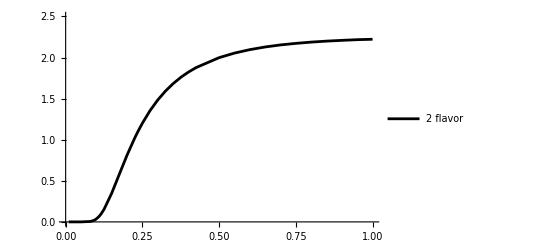

```mathematica
t1=ListLinePlot[{{0.01,d0},{0.05,d1},{0.08,d18},{0.09,d19},{0.095,d20},{0.1,d2},{0.108,d26},{0.115,d25},{0.125,d24},{0.15,d3},{0.175,d23},{0.2,d4},{0.225,d9},{0.235,d11},{0.25,d5},{0.275,d12},{0.3,d6},{0.325,d13},{0.35,d7},{0.375,d14},{0.38,d16},{0.4,d8},{0.425,d15},{0.5,d22},{0.55,d28},{0.6,d29},{0.65,d30},{0.7,d31},{0.75,d32},{0.8,d33},{0.85,d34},{0.9,d35},{0.95,d36},{1,d37}},PlotRange->{{0,1},{0,2.5}},BaseStyle->{Black,FontSize->20},PlotLegends->Placed[LineLegend[{"2 flavor"},LabelStyle->{FontSize->15}],{0.2,0.9}],FrameLabel->{Style["T(GeV)",20,Black,Italic],Style["D/\!\(\*SubscriptBox[\(D\), \(SYM\)]\)",20,Black,Italic]}]
```

```mathematica
(*假设你的数据点如下*)data={{{{0.01,d0},{0.05,d1},{0.08,d18},{0.09,d19},{0.095,d20},{0.1,d2},{0.108,d26},{0.115,d25},{0.125,d24},{0.15,d3},{0.175,d23},{0.2,d4},{0.225,d9},{0.235,d11},{0.25,d5},{0.275,d12},{0.3,d6},{0.325,d13},{0.35,d7},{0.375,d14},{0.38,d16},{0.4,d8},{0.425,d15},{0.5,d22},{0.55,d28},{0.6,d29},{0.65,d30},{0.7,d31},{0.75,d32},{0.8,d33},{0.85,d34},{0.9,d35},{0.95,d36},{1,d37}}}};

(*创建插值函数*)f=Interpolation[data];

(*计算插值函数的导数，使用数值导数以确保稳定性*)
df[x_]:=(f[x+10^-5]-f[x])/10^-5;

(*使用 NMaximize 找到导数的最大值及其对应的 x 值*)
maxSlopeResult=NMaximize[{df[x],0.1<=x<=0.3},x];

(*输出结果*)
maxSlopeResult
```

Interpolation::innd: {{{{0.01,1.53897×10^-25},{0.05,0.0000213761},{0.08,0.00525274},{0.09,0.0155061},{0.095,0.0243419},{0.1,«20»},{0.108,«20»},{0.115,0.0942893},{0.125,0.151961},{0.15,0.3485},«24»}}} 中的第一个参数不包含数据和坐标列表.

NMaximize::nnum: 函数值 -100000 (-Interpolation[{{{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«24»}}}][0.109146]+Interpolation[{{{{0.01,1.53897×10^-25},{0.05,0.0000213761},{0.08,0.00525274},«6»,{0.15,0.3485},«24»}}}][«20»]) 不是一个位于 {x} = {0.109146} 的数.

NMaximize[{100000 (-Interpolation[{{{{0.01,1.53897×10^-25},{0.05,0.0000213761},{0.08,0.00525274},{0.09,0.0155061},{0.095,0.0243419},{0.1,0.0363221},{0.108,0.062942},{0.115,0.0942893},{0.125,0.151961},{0.15,0.3485},{0.175,0.58125},{0.2,0.811626},{0.225,1.02023},{0.235,1.09598},{0.25,1.20093},{0.275,1.35444},{0.3,1.48314},{0.325,1.5913},{0.35,1.68193},{0.375,1.75834},{0.38,1.77209},{0.4,1.82282},{0.425,1.87765},{0.5,1.99873},{0.55,2.05416},{0.6,2.09612},{0.65,2.12875},{0.7,2.15372},{0.75,2.17245},{0.8,2.18794},{0.85,2.19992},{0.9,2.20914},{0.95,2.21745},{1,2.22257}}}}][x]+Interpolation[{{{{0.01,1.53897×10^-25},{0.05,0.0000213761},{0.08,0.00525274},{0.09,0.0155061},{0.095,0.0243419},{0.1,0.0363221},{0.108,0.062942},{0.115,0.0942893},{0.125,0.151961},{0.15,0.3485},{0.175,0.58125},{0.2,0.811626},{0.225,1.02023},{0.235,1.09598},{0.25,1.20093},{0.275,1.35444},{0.3,1.48314},{0.325,1.5913},{0.35,1.68193},{0.375,1.75834},{0.38,1.77209},{0.4,1.82282},{0.425,1.87765},{0.5,1.99873},{0.55,2.05416},{0.6,2.09612},{0.65,2.12875},{0.7,2.15372},{0.75,2.17245},{0.8,2.18794},{0.85,2.19992},{0.9,2.20914},{0.95,2.21745},{1,2.22257}}}}][1/100000+x]),0.1≤x≤0.3},x]

NMaximize::nnum: 函数值 -100000 (-Interpolation[{{{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«14»}}}][0.109146]+Interpolation[{{{{0.03,5.97552×10^-35},{0.05,3.27222×10^-7},{0.08,1.70091×10^-43},«5»,{0.125,0.0355756},{0.15,0.0942373},«14»}}}][0.109156]) 不是一个位于 {x} = {0.109146} 的数.

Interpolation::innd: {{{{0.03,5.97552×10^-35},{0.05,3.27222×10^-7},{0.08,1.70091×10^-43},{0.09,9.50832×10^-39},{0.095,9.48736×10^-37},{0.1,0.00658589},{0.108,0.0129285},{0.115,0.0208441},{0.125,0.0355756},{0.15,0.0942373},«14»}}} 中的第一个参数不包含数据和坐标列表.

NMaximize::nnum: 函数值 -100000 (-Interpolation[{{{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«14»}}}][0.109146]+Interpolation[{{{{0.03,5.97552×10^-35},{0.05,3.27222×10^-7},{0.08,1.70091×10^-43},{0.09,9.50832×10^-39},{0.095,9.48736×10^-37},{0.1,0.00658589},{0.115,0.0208441},{0.125,0.0355756},{0.15,0.0942373},{0.175,0.164276},«14»}}}][0.109156]) 不是一个位于 {x} = {0.109146} 的数.

Interpolation::innd: {{{{0.03,5.97552×10^-35},{0.05,3.27222×10^-7},{0.08,1.70091×10^-43},{0.09,9.50832×10^-39},{0.095,9.48736×10^-37},{0.1,0.00658589},{0.115,0.0208441},{0.125,0.0355756},{0.15,0.0942373},{0.175,0.164276},«14»}}} 中的第一个参数不包含数据和坐标列表.

FindMaximum::nrnum: 函数值 -Interpolation[{{{0.03,2.1773×10^-23},{0.05,0.0000358042},{0.08,4.83474×10^-29},{0.09,6.68613×10^-26},«3»,{0.2,0.190334},{0.225,0.230519},{0.235,0.244723},«11»}}]'[0.2] 不是位于 {x} = {0.2} 的一个实数.

Interpolation::inder: {0.09,6.68613×10^-26} 的阶数为 2 的导数不是一个维度为 2 的阶数为 2 的张量.

FindMaximum::nrnum: 函数值 0.+20. (d3-d4)-0.05 (40. (20. (d3+Times[«2»])+13.3333 (Times[«2»]+d9))-0.714286 (11.7647 (Times[«2»]+Times[«2»])-40. (Times[«2»]+Times[«2»]))) 不是位于 {x} = {0.2} 的一个实数.